```mathematica
(* Michael Barile *)
(* STAT 786 *)
(* HW #3 *)


(* initial values of x and y and deltat set to .01 *)
xInit=0.101; 
yInit=0.8;
deltat=.01;
tvec=Table[(i-1)*deltat,{i,5001}];
xvec={xInit};
yvec={yInit};

(* defining functions *)
f[x_,y_]:=x-2*x^2-x*y;
g[x_,y_]:=-0.1*y+x*y;

(* 4th order Runge-Kutta for 5000 iterations *)
For[i=1,i≤5000,++i,
m0=f[xvec[[i]],yvec[[i]]]*deltat;
k0=g[xvec[[i]],yvec[[i]]]*deltat;
m1=f[xvec[[i]]+(1/2)*m0,yvec[[i]]+(1/2)*k0]*deltat;
k1=g[xvec[[i]]+(1/2)*m0,yvec[[i]]+(1/2)*k0]*deltat;
m2=f[xvec[[i]]+(1/2)*m1,yvec[[i]]+(1/2)*k1]*deltat;
k2=g[xvec[[i]]+(1/2)*m1,yvec[[i]]+(1/2)*k1]*deltat;
m3=f[xvec[[i]]+m2,yvec[[i]]+k2]*deltat;
k3=g[xvec[[i]]+m2,yvec[[i]]+k2]*deltat;
AppendTo[xvec,xvec[[i]]+(1/6)*(m0+2*m1+2*m2+m3)];
AppendTo[yvec,yvec[[i]]+(1/6)*(k0+2*k1+2*k2+k3)];
];

points=Table[{xvec[[i]],yvec[[i]]},{i,Length[xvec]}];
(* plot of y as a function x *)
```

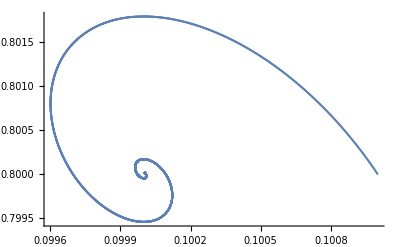

```mathematica
ListPlot[points,PlotRange->All]
```

```mathematica
xpoints=Table[{tvec[[i]],xvec[[i]]},{i,Length[xvec]}] ;
ypoints=Table[{tvec[[i]],yvec[[i]]},{i,Length[yvec]}] ;
```

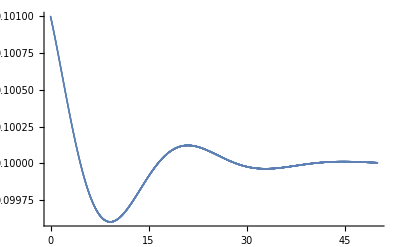

```mathematica
ListPlot[xpoints,PlotRange->All]
(* plot of x as a function of t, the Prey for 5000 iterations *)
```

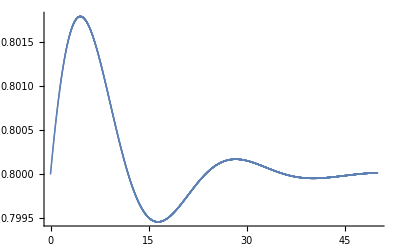

```mathematica
ListPlot[ypoints,PlotRange->All]
(* plot of y as a function of t, the Predator for 5000 iterations *)
```